```mathematica
ClearAll["Global`*"];Clear[Derivative];
```

```mathematica
Import[NotebookDirectory[]<>"lattice.wl"];
```

```mathematica
lattice=getLattice[3,2];
```

```mathematica
VertexList[lattice];
```

```mathematica
Length[%]
```

9

```mathematica
EdgeList[lattice];
```

```mathematica
Length[%]
```

12

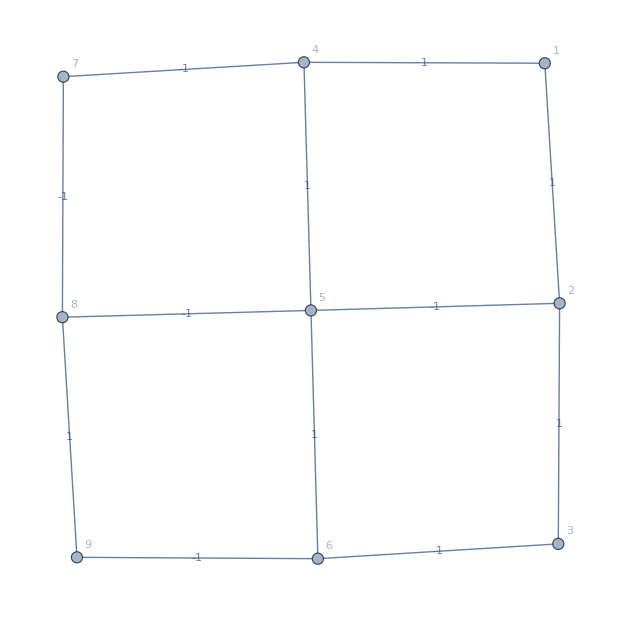

```mathematica
lattice=Fold[SetProperty[{#1,#2},VertexLabels->#2]&,lattice,VertexList[lattice]];

lattice=Fold[SetProperty[{#1,#2},EdgeLabels->PropertyValue[{#1,#2},EdgeCapacity]]&,lattice,EdgeList[lattice]]
```